```mathematica
(* For a pure state, the time evolution of the wigner function is simulated using Moyal formalism*)
(*Define the PDE*)pde=D[W[r,t],t]==2*W[r,t]+(r+1/(2*Clip[r,{0.1^10,Infinity}]))*D[W[r,t],r]+1/2*D[W[r,t],{r,2}];

(*Define the boundary conditions*)
boundaryConditions={W[20,t]==0,(*W[x=20,t]=0*)Derivative[1,0][W][0,t]==0 (*dW/dx is 0 at x=0 for all t*)};

(*Define the initial condition*)
initialCondition=W[r,0]== 2*Exp[-2*r^2]*LaguerreL[6,0,4*r^2]/Pi; (*You can change this as per your requirement*)

(*Solve the PDE*)
sol=NDSolve[{pde,boundaryConditions,initialCondition},W,{r,0,20},{t,0,10}];

(*Plot the solution at t=1*)
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
Manipulate[Plot[W[r,t]/. sol,{r,0,20},PlotRange->{-0.4,0.7}],{t,0,1}]
```

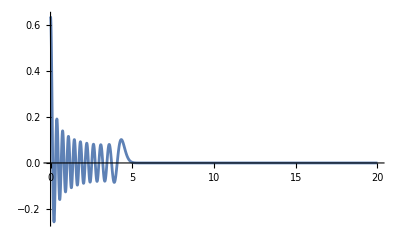

```mathematica
Plot[2*Exp[-2*r^2]*LaguerreL[20,0,4*r^2]/Pi, {r,0,20},PlotRange->All]
```